```mathematica
Options[EliminatePoints]={
ProfileParameters->{ProfileRadius->0.05},
ProfileFunction->(Chop[Exp[-(#1-#2).(#1-#2)/ProfileRadius^2]/.#3,10^-5]&),
Seed->1,
InitialTemp->1,
FinalTemp->0.001,
MaxIterations->1000,
VicinityStack->False,
FixedPointIndices->{}
};
```

```mathematica
(* An algorithm to select evenly spaced points *)
EliminatePoints[pts_,OptionsPattern[]]:=Module[{pmat,qmat,target,x,seed,v,t0,t,targetLog,prob,iter,fluc,temp,temp0,best,tbest,flexindices,stack,stackindex,seqtrial},
pmat=Outer[OptionValue[ProfileFunction][#1,#2,OptionValue[ProfileParameters]]&,pts,pts,1];
qmat=SparseArray[2DiagonalMatrix[Diagonal[pmat]]-pmat];
target[x_]:=x.qmat.x;
seed=OptionValue[Seed];
If[Head[seed]=!=List,seed=Map[seed&,pts]];
Scan[(seed[[#]]=1)&,OptionValue[FixedPointIndices]];
flexindices=RandomSample[Complement[Range[Length[pts]],OptionValue[FixedPointIndices]]];
t0=target[seed];
tbest=t0;
best=seed;
targetLog={{0,t0}};
iter=1;
seqtrial=0;
stackindex=0;
temp0=OptionValue[InitialTemp];
Print[ProgressIndicator[Dynamic[iter],{0,OptionValue[MaxIterations]}]];
While[iter<OptionValue[MaxIterations],
temp=temp0*Exp[iter/OptionValue[MaxIterations]*Log[OptionValue[FinalTemp]]];
If[stackindex==0,
fluc=flexindices[[Mod[seqtrial,Length[flexindices]]+1]];
seqtrial++,
fluc=stack[[stackindex]];
stackindex--;
];
v=seed; v[[fluc]]=1-v[[fluc]];
t=target[v];
If[t>=t0,seed=v; t0=t,
(* Metropolis step *)
prob=Exp[-(t0-t)/temp];
If[Random[]<prob,(* stepping down*)
If[t0>tbest,best=seed;tbest=t0];
seed=v; t0=t;
If[stackindex==0 && OptionValue[VicinityStack],
 (* set up a stack of indices we would like to try switching next, because they are close *)
stack=qmat[[fluc]]+qmat[[All,fluc]];
stack=SortBy[Most[ArrayRules[stack]],-#[[2]]&];
If[Length[stack]≥2,
stack=Rest[stack][[All,1,1]];
stack=Select[stack,MemberQ[flexindices,#]&];
stackindex=Length[stack];
];
];
];
];
AppendTo[targetLog,{iter,t0}];
iter++;
];
(*Print[maxtrials];*)
{Pick[pts,best/.{0->False,1->True}],targetLog}
];
```

```mathematica
fname = "~/mnt/qcdhome/mywork/remot/tmdanalys/mathematica/eliminatepoints.m";
DeleteFile[fname];
Save[fname,{EliminatePoints}]
```

DeleteFile::fdnfnd: Directory or file "/Users/hariprashadravikumar/mnt/qcdhome/mywork/remot/tmdanalys/mathematica/eliminatepoints.m" not found.

Save::noopen: Cannot open ~/mnt/qcdhome/mywork/remot/tmdanalys/mathematica/eliminatepoints.m.

$Failed

```mathematica
Definition[EliminatePoints]
```

EliminatePoints[pts_,OptionsPattern[]]:=Module[{pmat,qmat,target,x,seed,v,t0,t,targetLog,prob,iter,fluc,temp,temp0,best,tbest,flexindices,stack,stackindex,seqtrial},pmat=Outer[OptionValue[ProfileFunction][#1,#2,OptionValue[ProfileParameters]]&,pts,pts,1];qmat=SparseArray[2 DiagonalMatrix[Diagonal[pmat]]-pmat];target[x_]:=x.qmat.x;seed=OptionValue[Seed];If[Head[seed]=!=List,seed=(seed&)/@pts];Scan[(seed⟦#1⟧=1)&,OptionValue[FixedPointIndices]];flexindices=RandomSample[Complement[Range[Length[pts]],OptionValue[FixedPointIndices]]];t0=target[seed];tbest=t0;best=seed;targetLog={{0,t0}};iter=1;seqtrial=0;stackindex=0;temp0=OptionValue[InitialTemp];Print[ProgressIndicator[,{0,OptionValue[MaxIterations]}]];While[iter<OptionValue[MaxIterations],temp=temp0 Exp[(iter Log[OptionValue[FinalTemp]])/OptionValue[MaxIterations]];If[stackindex==0,fluc=flexindices⟦Mod[seqtrial,Length[flexindices]]+1⟧;seqtrial++,fluc=stack⟦stackindex⟧;stackindex--;];v=seed;v⟦fluc⟧=1-v⟦fluc⟧;t=target[v];If[t≥t0,seed=v;t0=t,prob=Exp[-(t0-t)/temp];If[Random[]<prob,If[t0>tbest,best=seed;tbest=t0];seed=v;t0=t;If[stackindex==0&&OptionValue[VicinityStack],stack=qmat⟦fluc⟧+qmat⟦All,fluc⟧;stack=SortBy[Most[ArrayRules[stack]],-#1⟦2⟧&];If[Length[stack]≥2,stack=Rest[stack]⟦All,1,1⟧;stack=Select[stack,MemberQ[flexindices,#1]&];stackindex=Length[stack];];];];];AppendTo[targetLog,{iter,t0}];iter++;];{Pick[pts,best/.{0→False,1→True}],targetLog}]
 
Options[EliminatePoints]={ProfileParameters→{ProfileRadius→0.05},ProfileFunction→(Chop[Exp[-((#1-#2).(#1-#2))/ProfileRadius^2]/.#3,1/10^5]&),Seed→1,InitialTemp→1,FinalTemp→0.001,MaxIterations→1000,VicinityStack→False,FixedPointIndices→{}}

```mathematica
Log[0.01]
```

-4.60517

```mathematica
Most[ArrayRules[SparseArray[{{1,0,0},{0,1,0},{1,1,0}}][[All,2]]]][[All,1,1]]
```

{2,3}

```mathematica
pts=RandomReal[{0,1},{200,2}];
```

```mathematica
elpts=EliminatePoints[pts,MaxIterations->10000,VicinityStack->False,FinalTemp->0.001,InitialTemp->1,FixedPointIndices->Range[10]];
```

General::munfl: Exp[-738.072] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-804.488] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-775.054] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

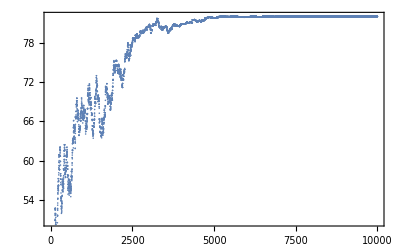

```mathematica
ListPlot[elpts[[2]],Frame->True,Axes->False,PlotRange->Automatic]
```

```mathematica
elpts[[2,-1]]
```

{9999,81.9972}

```mathematica
Length[elpts[[1]]]
```

104

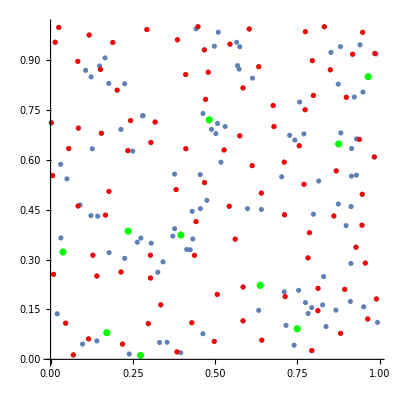

```mathematica
Show[ListPlot[pts],ListPlot[elpts[[1]],PlotStyle->Red],ListPlot[pts[[Range[10]]],PlotStyle->Green],AspectRatio->1]
```